```mathematica
(* Gaussian CDF *)
gaussianCDF[x_] := CDF[NormalDistribution[0, 1], x]

(* Gaussian PPF *)
gaussianPPF[x_] := Quantile[NormalDistribution[0, 1], x]
```

```mathematica
Subscript[L, X][x_,S_]:=x/(1-gaussianCDF[Log[S/K]/σ+1/2 σ]);
Subscript[L, Y][y_,S_]:=y/(K*gaussianCDF[Log[S/K]/σ-1/2 σ]);
X[y_,S_]:=Subscript[L, Y][y,S]*(1-gaussianCDF[Log[S/K]/σ+1/2 σ]);
Y[x_,S_]:=K*Subscript[L, X][x,S]*gaussianCDF[Log[S/K]/σ-1/2 σ];
Subscript[P, X][x_,L_]:=K*Exp[gaussianPPF[1-x/L]*σ-1/2 σ^2];
Subscript[P, Y][y_,L_]:=K*Exp[gaussianPPF[y/(K*L)]*σ+1/2 σ^2];
```

```mathematica
(* Constants *)
σ:=1;
K:=1;
γ:=1;
```

```mathematica
(* Initial X value *)
Subscript[x, 0]:=1;
(* Initial price *)
Subscript[S, 0]:=1;
(* Amount of Y for this price and X *)
Subscript[y, 0]:=Y[Subscript[x, 0],Subscript[S, 0]]
Print["Initial y: ", Subscript[y, 0]]
(* Liquidity *)
Subscript[L, 0]:=Subscript[L, X][Subscript[x, 0],Subscript[S, 0]]
Print["Initial L: ", Subscript[L, 0]]
```

Initial y: Erfc[1/(2 √2)]/(2 (1-1/2 Erfc[-1/(2 √2)]))

Initial L: 1/(1-1/2 Erfc[-1/(2 √2)])

```mathematica
(* Quck sanity checks *)
Print["This should print 1: ", Subscript[P, X][Subscript[x, 0],Subscript[L, 0]]]
Print["This should print 1: ", Subscript[P, Y][Subscript[y, 0],Subscript[L, 0]]]
```

This should print 1: 1

This should print 1: 1

```mathematica
(* Arb calculations *)
arbX[p_,x_,L_]:=(L*(1-gaussianCDF[Log[p/K]/σ+1/2 σ])-x)/(1+(γ-1)*(1-gaussianCDF[Log[p/K]/σ+1/2 σ])/(1-gaussianCDF[Log[Subscript[S, 0]/K]/σ+1/2 σ]));
arbY[p_,y_,L_]:=(K*L*gaussianCDF[Log[p/K]/σ-1/2 σ]-y)/(1+(γ-1)gaussianCDF[Log[p/K]/σ-1/2 σ]/gaussianCDF[Log[Subscript[S, 0]/K]/σ-1/2 σ]);
```

We are tendering the following amount of X:

Δ_X = 0.0114969

After applying the fee, we will have the following X reinvested:

δ_X = 0.

The effective amount of Y reinvested is:

δ_Y = 0.

The effective amount of liquidity reinvested is:

δ_L = 0.

The amount of Y the user will receive

Δ_Y = 0.0114393

The effective price the user paid is then:

P_eff = 0.994987

Computing the new L using new X reserve:

L_givenX = 3.2411

Computing the new L using new Y reserve:

L_givenY = 3.2411

Computing the new price given the new X reserve:

S = 0.99

Computing the new price given the new Y reserve:

S = 0.99

Profit is: 0.0000573405

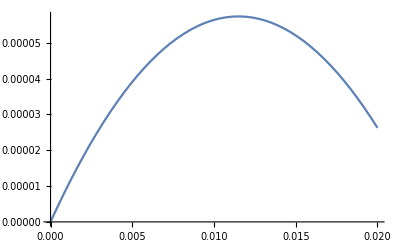

ConditionalExpression[-0.99+0.606531 ⅇ^(√2 InverseErfc[(1+v) Erfc[1/(2 √2)]]), 0≤1/2 (1+v) Erfc[1/(2 √2)]≤1]

Profit maximizing input is: 0.0114969

The profit from this trade is: 0.0000573405

```mathematica
(* Test a value that we got from above here *)
(*newPriceX:=0.985;*)
newPriceX:=0.99(*2047873705309300*);
tenderX:=arbX[newPriceX,Subscript[x, 0],Subscript[L, 0]] (*- 0.000156*);
(*tenderX:=0.1;*)
Print["We are tendering the following amount of X:"]
Print["Δ_X = ", tenderX]
Print["After applying the fee, we will have the following X reinvested:"]
Subscript[δ, Xx][Δ_]:=(1-γ)*Δ;
Print["δ_X = ", Subscript[δ, Xx][tenderX]]

(* Swap in X with fee chosen above *)
(*Subscript[δ, Lx][Δ_]:= Subscript[L, X][Subscript[δ, Xx][Δ],Subscript[S, 0]]*)
Subscript[δ, Lx][Δ_]:= Subscript[δ, Xx][Δ]*Subscript[L, 0]/Subscript[x, 0]
(* This can be simplified *)
Subscript[δ, Yx][Δ_]:=K*Subscript[δ, Lx][Δ]*gaussianCDF[Log[Subscript[S, 0]/K]/σ-1/2 σ]
Print["The effective amount of Y reinvested is:"]
Print["δ_Y = ", Subscript[δ, Yx][tenderX]]

Print["The effective amount of liquidity reinvested is:"]
Print["δ_L = ", Subscript[δ, Lx][tenderX]]

Print["The amount of Y the user will receive"]
Subscript[Δ, Y][Δ_]:=K*(Subscript[L, 0]+Subscript[δ, Lx][Δ])*gaussianCDF[-σ-gaussianPPF[(Subscript[x, 0]+Δ)/(Subscript[L, 0]+Subscript[δ, Lx][Δ])]]-Subscript[y, 0];
Print["Δ_Y = ", -Subscript[Δ, Y][tenderX]]

Print["The effective price the user paid is then:"]
Subscript[P, eff]:=(-Subscript[Δ, Y][tenderX])/tenderX;
Print["P_eff = ", Subscript[P, eff]]

(* What are the liquidities *)
Print["Computing the new L using new X reserve:"]
Subscript[L, givenX]:= Subscript[L, X][Subscript[x, 0]+Subscript[δ, Xx][tenderX], Subscript[S, 0]]
Print["L_givenX = ", Subscript[L, givenX]]

Print["Computing the new L using new Y reserve:"]
Subscript[L, givenY]:=Subscript[L, Y][Subscript[y, 0]+Subscript[δ, Yx][tenderX], Subscript[S, 0]]
Print["L_givenY = ", Subscript[L, givenY]]

Print["Computing the new price given the new X reserve:"]
(* Now what is the price? Should be 0.9 *)
Print["S = ", Subscript[P, X][Subscript[x, 0]+tenderX,Subscript[L, givenX]]]
Print["Computing the new price given the new Y reserve:"]
Print["S = ", Subscript[P, Y][Subscript[y, 0]+Subscript[Δ, Y][tenderX],Subscript[L, givenY]]]

(* How much do we profit? *)
profit:=(Subscript[P, eff]-Subscript[P, X][Subscript[x, 0]+tenderX,Subscript[L, givenX]])*tenderX
Print["Profit is: ", profit]

Subscript[P, effective][in_]:=(-Subscript[Δ, Y][in])/in;
arbProfit[in_]:=(Subscript[P, effective][in]-newPriceX)*in;
Plot[arbProfit[v], {v,0,0.02}]
FullSimplify[D[arbProfit[v],v]]
arbMaximizer:=ArgMax[{arbProfit[v],0<=v<=1},v];
Print["Profit maximizing input is: ", arbMaximizer];
Print["The profit from this trade is: ", arbProfit[arbMaximizer]]
```

```mathematica
(* Test a value that we got from above here *)
newPriceY:=1.1;
tenderY:=arbY[newPriceY,Subscript[y, 0],Subscript[L, Y][Subscript[y, 0],Subscript[S, 0]]]
Print["We are tendering the following amount of Y:"]
Print["Δ_Y = ", tenderY]
Print["After applying the fee, we will have the following X reinvested:"]
Subscript[δ, Yy][Δ_]:=(1-γ)*Δ;
Print["δ_Y = ", Subscript[δ, Yy][tenderY]]

(* Swap in X with fee chosen above *)
(*Subscript[δ, Ly][Δ_]:= Subscript[L, Y][Subscript[δ, Yy][Δ],Subscript[S, 0]]*)
Subscript[δ, Ly][Δ_]:= Subscript[δ, Yy][Δ]*Subscript[L, 0]/Subscript[y, 0]
(* This can be simplified *)
Subscript[δ, Xy][Δ_]:=Subscript[δ, Ly][Δ]*(1-gaussianCDF[Log[Subscript[S, 0]/K]/σ+1/2 σ])
Print["The effective amount of Y reinvested is:"]
Print["δ_x = ", Subscript[δ, Xy][tenderY]]

Print["The effective amount of liquidity reinvested is:"]
Print["δ_L = ", Subscript[δ, Ly][tenderY]]

Print["The amount of X the user will receive"]
Subscript[Δ, X][Δ_]:=(Subscript[L, 0]+Subscript[δ, Ly][Δ])*gaussianCDF[-σ-gaussianPPF[(Subscript[y, 0]+Δ)/(K*(Subscript[L, 0]+Subscript[δ, Ly][Δ]))]]-Subscript[x, 0];
Print["Δ_X = ", -Subscript[Δ, X][tenderY]]

Print["The effective price the user paid is then:"]
Print["P_eff = ", -tenderY/(Subscript[Δ, X][tenderY])]

(* What are the liquidities *)
Print["Computing the new L using new X reserve:"]
Subscript[L, givenX]:= Subscript[L, X][Subscript[x, 0]+Subscript[δ, Xx][tenderY], Subscript[S, 0]]
Print["L_givenX = ", Subscript[L, givenX]]

Print["Computing the new L using new Y reserve:"]
Subscript[L, givenY]:=Subscript[L, Y][Subscript[y, 0]+Subscript[δ, Yy][tenderY], Subscript[S, 0]]
Print["L_givenY = ", Subscript[L, givenY]]

Print["Computing the new price given the new X reserve:"]
(* Now what is the price? Should be 0.9 *)
Print["S = ", Subscript[P, X][Subscript[x, 0]+Subscript[Δ, X][tenderY],Subscript[L, givenX]]]
Print["Computing the new price given the new Y reserve:"]
Print["S = ", Subscript[P, Y][Subscript[y, 0]+tenderY,Subscript[L, givenY]]]
```

We are tendering the following amount of Y:

Δ_Y = 0.111591

After applying the fee, we will have the following X reinvested:

δ_Y = 0.000334773

The effective amount of Y reinvested is:

δ_x = 0.000334773

The effective amount of liquidity reinvested is:

δ_L = 0.00108503

The amount of X the user will receive

Δ_X = 0.105748

The effective price the user paid is then:

P_eff = 1.05526

Computing the new L using new X reserve:

L_givenX = 3.24218

Computing the new L using new Y reserve:

L_givenY = 3.24218

Computing the new price given the new X reserve:

S = 1.1

Computing the new price given the new Y reserve:

S = 1.1